# bounded double integrator controller

## V̇ not negative definite

```mathematica
σσ[x_,σ_]:=x/(√(1+(x.x)/σ^2))
uDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-kp 1/(√(1+(v.v)/σd^2))σσ[p,σp]-kd σσ[v,σd];
VDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=kp σp^2( √((p.p)/σp^2+1)-1)  +1/3 (1+(v.v)/σd^2)^(3/2) σd^2 

JoinAs[A11_,A12_,A21_,A22_]:=Join[Join[A11,A12,2],Join[A21,A22,2]]
WDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-kd v.v
```

```mathematica
(*check that indeed V̇(p,v)=W(p,v)*)
error[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=WDIA[p,v,{kp,σp,kd,σd,β}]-D[VDIA[p,v,{kp,σp,kd,σd,β}],{Join[p,v]}].Join[v,uDIA[p,v,{kp,σp,kd,σd,β}]]
error[{p1,p2,p3},{v1,v2,v3},{kp,σp,kd,σd,β}]//Simplify
```

0

## V̇ negative definite

```mathematica
σσ[x_,σ_]:=x/(√(1+(x.x)/σ^2))
uDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-kp 1/(√(1+(v.v)/σd^2))σσ[p,σp]-kd σσ[v,σd];
VDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=kp σp^2( √((p.p)/σp^2+1)-1)  +β σσ[p,σp].σσ[v,σd]+1/3 σd^2((√(1+(v.v)/σd^2))^3 -1)

JoinAs[A11_,A12_,A21_,A22_]:=Join[Join[A11,A12,2],Join[A21,A22,2]]
Ws[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=1/(√(1+(v.v)/σd^2))JoinAs[
kp β D[σσ[v,σd],{v}],
1/2 β kd D[σσ[v,σd],{v}],1/2 β kd D[σσ[v,σd],{v}],
√(1+(v.v)/σd^2)kd IdentityMatrix[Length[p]]-β  D[σσ[p,σp],{p}] 
]
WDIA[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=-#1.Ws[p,v,{kp,σp,kd,σd,β}].#1&[Join[σσ[p,σp],v]];
```

```mathematica
(*check that indeed V̇(p,v)=W(p,v)*)
error[p_,v_,{kp_,σp_,kd_,σd_,β_}]:=WDIA[p,v,{kp,σp,kd,σd,β}]-D[VDIA[p,v,{kp,σp,kd,σd,β}],{Join[p,v]}].Join[v,uDIA[p,v,{kp,σp,kd,σd,β}]]
error[{p1,p2,p3},{v1,v2,v3},{kp,σp,kd,σd,β}]//Simplify
```

0

## “v^2/2 term”

```mathematica
Integrate[√(1+v^2/σd^2)v,v]-1/3 σd^2((√(1+v^2/σd^2))^3-0)//Simplify
```

0

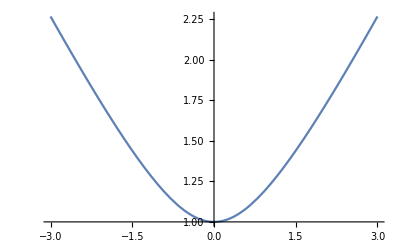

```mathematica
Plot[(1/3 σd^2((√(1+v^2/σd^2))^3 -1))/(v^2/2)/.{σd-> 1},{v,-3,3}]
```

```mathematica
Series[1/3 σd^2((√(1+v^2/σd^2))^3 -1),{v,0,2}]
```

v^2/2+O[v]^3

## bound on input

```mathematica
D[uDIA[{p},{v},{kp,σp,kd,σd,β}],v][[1]]//Simplify
sol=Solve[D[uDIA[{p},{v},{kp,σp,kd,σd,β}],v][[1]]==0,v]//Simplify
(*D[uDIA[{p},{v},{kp,σp,kd,σd,β}],v][[1]]/.sol[[1]]//Simplify*)
Simplify[Limit[uDIA[{p},{v},{kp,σp,kd,σd,β}][[1]]/.sol[[1]]//Simplify,p-> +Infinity],σp>0]
Simplify[Limit[uDIA[{p},{v},{kp,σp,kd,σd,β}][[1]]/.sol[[1]]//Simplify,p-> -Infinity],σp>0]
```

(kp p v-kd σd^2 √(1+p^2/σp^2))/(√(1+v^2/σd^2) (v^2+σd^2) √(1+p^2/σp^2))

{{v→(kd σd^2 √(1+p^2/σp^2))/(kp p)}}

-kp √(1+(kd^2 σd^2)/(kp^2 σp^2)) σp

kp √(1+(kd^2 σd^2)/(kp^2 σp^2)) σp

# simpler

## double integrator control law

### some preliminaries

```mathematica
VDI[p_,v_]:=1/2{p,v}.{{1,γ1},{γ1,γ2}}.{p,v}
CoefficientList[D[VDI[p,v],{{p,v}}].{v,-kp p-kd v},p]//Simplify
CoefficientList[D[VDI[p,v],{{p,v}}].{v,-kp p-kd v},v]//Simplify
```

{v^2 (γ1-kd γ2),-v (-1+kd γ1+kp γ2),-kp γ1}

{-kp p^2 γ1,-p (-1+kd γ1+kp γ2),γ1-kd γ2}

```mathematica
sol=Solve[-1+kd γ1+kp γ2==0&&γ1-kd γ2==- Γ,{γ1,γ2}]/.{Γ-> 1/2 kd/kp}//Simplify;
(*determinant of matrix in Lyapunov function*)
γ2-γ1^2/.sol[[1]]//Simplify
```

(2 kd^4+5 kd^2 kp+4 kp^2)/(4 kp (kd^2+kp)^2)

```mathematica
sol[[1]]
```

{γ1→kd/(2 (kd^2+kp)),γ2→(kd^2+2 kp)/(2 kd^2 kp+2 kp^2)}

### lyapunov function

```mathematica
Clear[VDI]
```

```mathematica
VDI[p_,v_]:=Evaluate[1/2{p,v}.{{1,γ1},{γ1,γ2}}.{p,v}/.sol[[1]]]
WDI[p_,v_]:=Evaluate[D[VDI[p,v],{{p,v}}].{v,-kp p-kd v}]

(*VI is positive definite*)
{γ1,γ2,γ2-γ1^2}/.sol[[1]]//Simplify
(*WI is negative definite*)
WDI[p,v]-(-{p,v}.{{(kd kp)/(2 (kd^2+kp)),0},{0,kd/(2 kp)}}.{p,v})//Simplify
```

{kd/(2 (kd^2+kp)),(kd^2+2 kp)/(2 kd^2 kp+2 kp^2),(2 kd^4+5 kd^2 kp+4 kp^2)/(4 kp (kd^2+kp)^2)}

0

# more evolved

```mathematica
u=-kp#1/(√(1+(#1.#1)/σp^2))-kv#2/(√(1+(#2.#2)/σv^2))&[{px,py,pz},{vx,vy,vz}];
V=kp σp^2( √((#1.#1)/σp^2+1)-1)  +β (#1/(√(1+(#1.#1)/σp^2))).(#2/(√(1+(#2.#2)/σv^2)))+(#2.#2)/2&[{px,py,pz},{vx,vy,vz}];
```

```mathematica
JoinAs[A11_,A12_,A21_,A22_]:=Join[
Join[A11,A12,2],
Join[A21,A22,2]
]
```

```mathematica
VM=JoinAs[
σp^2 kp(√((#1.#1)/σp^2+1)-1)/(#1.#1) IdentityMatrix[3],
1/2 β 1/(√(1+(#1.#1)/σp^2))1/(√(1+(#2.#2)/σv^2))IdentityMatrix[3],
1/2 β 1/(√(1+(#1.#1)/σp^2))1/(√(1+(#2.#2)/σv^2))IdentityMatrix[3],
1/2 IdentityMatrix[3]
]&[{px,py,pz},{vx,vy,vz}];
```

```mathematica
V-(Join[#1,#2].VM.Join[#1,#2])&[{px,py,pz},{vx,vy,vz}]//Simplify
```

0

```mathematica
σp^2 kp(√((#1.#1)/σp^2+1)-1)/(#1.#1)-(1/2)^-1(1/2 β 1/(√(1+(#1.#1)/σp^2))1/(√(1+(#2.#2)/σv^2)))^2>0
σp^2 kp(√((#1.#1)/σp^2+1)-1)/(#1.#1)-1/2( β 1/(√(1+(#1.#1)/σp^2))1/(√(1+(#2.#2)/σv^2)))^2>0
σp^2 kp(√((#1.#1)/σp^2+1)-1)/(#1.#1)>1/2( β 1/(√(1+(#1.#1)/σp^2))1/(√(1+(#2.#2)/σv^2)))^2
(σp^2 kp)/β^2>1/2 (#1.#1)/(√((#1.#1)/σp^2+1)-1) 1/(1+(#1.#1)/σp^2)1/(1+(#2.#2)/σv^2)
β^2<2 σp^2 kp (√((#1.#1)/σp^2+1)-1)/(#1.#1) (1+(#1.#1)/σp^2)(1+(#2.#2)/σv^2)
(*β^2<2 σp^2 kp (√((#1.#1)/σp^2+1)-1 )(1/(#1.#1)+1/σp^2)(1+(#2.#2)/σv^2)*)
β^2<kp (√((#1.#1)/σp^2+1)-1)/((#1.#1)/2) (σp^2 +#1.#1)(1+(#2.#2)/σv^2)
β^2<kp<kp (√((#1.#1)/σp^2+1)-1)/((#1.#1)/2) (σp^2 +#1.#1)(1+(#2.#2)/σv^2)
```

β^2<kp

DirectedInfinity[√(1/Sign[σp]^2)]

1

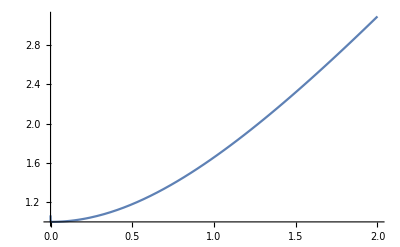

```mathematica
Limit[(√(x^2/σp^2+1)-1)/(x^2/2) (σp^2 +x^2),x-> Infinity]
Limit[(√(x^2/σp^2+1)-1)/(x^2/2) (σp^2 +x^2),x->0]
Plot[(√(x^2/σp^2+1)-1)/(x^2/2) (σp^2 +x^2)/.σp->1 ,{x,0,2}]
```

```mathematica
kv IdentityMatrix[3]-β D[#1/(√(1+(#1.#1)/σp^2)),{#1}]-1/2 β kv D[#2/(√(1+(#2.#2)/σv^2)),{#2}](kp β √(1+(#2.#2)/σv^2)D[#2/(√(1+(#2.#2)/σv^2)),{#2}])^-1 1/2 β kv D[#2/(√(1+(#2.#2)/σv^2)),{#2}]>0
kv IdentityMatrix[3]-β D[#1/(√(1+(#1.#1)/σp^2)),{#1}]-1/4(β^2 kv^2)/(kp β √(1+(#2.#2)/σv^2))  D[#2/(√(1+(#2.#2)/σv^2)),{#2}](D[#2/(√(1+(#2.#2)/σv^2)),{#2}])^-1 D[#2/(√(1+(#2.#2)/σv^2)),{#2}]>0
kv IdentityMatrix[3]- β (1+1/4 kv^2/kp 1/(√(1+(#2.#2)/σv^2))  )D[#1/(√(1+(#1.#1)/σp^2)),{#1}]>0
β (1+1/4 kv^2/kp 1/(√(1+(#2.#2)/σv^2))  )Norm[D[#1/(√(1+(#1.#1)/σp^2)),{#1}]]<kv 
β <kv/(1+1/4 kv^2/kp 1/(√(1+(#2.#2)/σv^2)))1/Norm[D[#1/(√(1+(#1.#1)/σp^2)),{#1}]]
β <kv/(1+1/4 kv^2/kp)<kv/(1+1/4 kv^2/kp 1/(√(1+(#2.#2)/σv^2)))1/Norm[D[#1/(√(1+(#1.#1)/σp^2)),{#1}]]
```

β<min(√kp,kv/(1+1/4 kv^2/kp))

```mathematica
Ws=1/(√(1+(#2.#2)/σv^2))JoinAs[
kp β √(1+(#2.#2)/σv^2)D[#2/(√(1+(#2.#2)/σv^2)),{#2}],
1/2 β kv D[#2/(√(1+(#2.#2)/σv^2)),{#2}],
1/2 β kv D[#2/(√(1+(#2.#2)/σv^2)),{#2}],
kv IdentityMatrix[3]-β D[#1/(√(1+(#1.#1)/σp^2)),{#1}]
]&[{px,py,pz},{vx,vy,vz}];
```

```mathematica
D[V,{#1}].#2+D[V,{#2}].u-(-Join[#1/(√(1+(#1.#1)/σp^2)),#2].Ws.Join[#1/(√(1+(#1.#1)/σp^2)),#2])&[{px,py,pz},{vx,vy,vz}]/.Thread[#->RandomReal[{-4,4},Length[#]]&[{px,py,pz,vx,vy,vz,kp,kv,σp,σv,β}]]//N//Chop
```

0

```mathematica
(*step 1*)
kp σp(#1.#2)/(√(#1.#1+σp^2))  +β ((#2/(√(1+(#2.#2)/σv^2))).D[#1/(√(1+(#1.#1)/σp^2)),#1].#2+(#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].(-kp#1/(√(1+(#1.#1)/σp^2))-kv#2/(√(1+(#2.#2)/σv^2))))+#2.(-kp#1/(√(1+(#1.#1)/σp^2))-kv#2/(√(1+(#2.#2)/σv^2)))  
(*step 2*)
β ((#2/(√(1+(#2.#2)/σv^2))).D[#1/(√(1+(#1.#1)/σp^2)),#1].#2+(#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].(-kp#1/(√(1+(#1.#1)/σp^2))-kv#2/(√(1+(#2.#2)/σv^2))))+#2.(-kv#2/(√(1+(#2.#2)/σv^2)))
  -kv 1/(√(1+(#2.#2)/σv^2))(β (1/-kv#2.D[#1/(√(1+(#1.#1)/σp^2)),#1].#2+(#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].(kp/kv 1/(√(1+(#2.#2)/σv^2))#1/(√(1+(#1.#1)/σp^2))+#2))+#2.#2)
  (*step 3*)-kv 1/(√(1+(#2.#2)/σv^2))(β kp/kv 1/(√(1+(#2.#2)/σv^2)) (#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].(#1/(√(1+(#1.#1)/σp^2)))+β (#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].#2+#2.#2-β/kv#2.D[#1/(√(1+(#1.#1)/σp^2)),#1].#2)
(*step 4*)
-1/(√(1+(#2.#2)/σv^2))(β kp 1/(√(1+(#2.#2)/σv^2)) (#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].(#1/(√(1+(#1.#1)/σp^2)))+β kv (#1/(√(1+(#1.#1)/σp^2))).D[#2/(√(1+(#2.#2)/σp^2)),#2].#2+kv #2.#2-β#2.D[#1/(√(1+(#1.#1)/σp^2)),#1].#2)
```

#### β < kv/(1+kv^2/(4 kp))≤ min(√kp,kv/(1+kv^2/(4 kp))) note that β can be defined in simpler manner

```mathematica
Simplify[√kp-ωn/.{kv-> 2 ξ ωn,kp-> ωn^2},ωn>0]
Simplify[kv/(1+kv^2/(4 kp))-1/(1+(ξ-1)^2/(2 ξ))ωn/.{kv-> 2 ξ ωn,kp-> ωn^2}]
```

0

0

# bounded backstepping?

```mathematica
X1[x1_,x2_]:=x2
x2cl[x1_,x2_]:=-f[x2]σ1[x1]
V1[x1_]:=x1^2/2
W1[x1_,x2_]:=-f[x2]x1 σ1[x1]
D[V1[x1],x1] X1[x1,x2]-(W1[x1,x2]+x1(x2-x2cl[x1,x2]))//Simplify
e2[x1_,x2_]:=x2-x2cl[x1,x2]
```

0

```mathematica
(*X2[{x1_,x2_},x3_]:={X1[x1,x2],x3-(-σ1'[x1]x2)}*)
X2[{x1_,e2_},x3_]:={X1[x1,x2cl[x1,x2]+e2],x3-(D[x2cl[x1,x2],x1]x2+D[x2cl[x1,x2],x2]x3)}
x3cl[x1_,e1_]:=-σ2[e1]-σ1'[x1](x2cl[x1]+e1)-(1+V1[x1]/V10)^-1 x1
V2[x1_,e1_]:=V10 Log[(V1[x1]+V10)/V10]+e1^2/2
W2[x1_,e1_]:=(1+V1[x1]/V10)^-1 W1[x1]-e1 σ2[e1]
D[V2[x1,e1],{{x1,e1}}] .X2[{x1,e1},x3]-(W2[x1,e1]+e1(x3-x3cl[x1,e1]))//Simplify
```

0

```mathematica
(*X2[{x1_,x2_},x3_]:={X1[x1,x2],x3-(-σ1'[x1]x2)}*)
X2[{x1_,e2_},x3_]:={X1[x1,x2cl[x1]+e2],x3-(-σ1'[x1](x2cl[x1]+e2))}
x3cl[x1_,e1_]:=-σ2[e1]-σ1'[x1](x2cl[x1])-(1+V1[x1]/V10)^-1 x1
V2[x1_,e1_]:=V10 Log[(V1[x1]+V10)/V10]+e1^2/2
W2[x1_,e1_]:=(1+V1[x1]/V10)^-1 W1[x1]-e1 σ2[e1]+e1 σ1'[x1] e1
D[V2[x1,e1],{{x1,e1}}] .X2[{x1,e1},x3]-(W2[x1,e1]+e1(x3-x3cl[x1,e1]))//Simplify
```

0

```mathematica
(*X2[{x1_,x2_},x3_]:={X1[x1,x2],x3-(-σ1'[x1]x2)}*)
X2[{x1_,x2_},x3_]:={X1[x1,x2],x3-(D[x2cl[x1,x2],x1]x2+D[x2cl[x1,x2],x2]x3)}
x3cl[x1_,e1_]:=-σ2[e1]-σ1'[x1](x2cl[x1]+e1)-(1+V1[x1]/V10)^-1 x1
V2[x1_,e1_]:=V10 Log[(V1[x1]+V10)/V10]+e1^2/2
W2[x1_,e1_]:=(1+V1[x1]/V10)^-1 W1[x1]-e1 σ2[e1]
D[V2[x1,e1],{{x1,e1}}] .X2[{x1,e1},x3]-(W2[x1,e1]+e1(x3-x3cl[x1,e1]))//Simplify
```